## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.

```mathematica
SetDirectory[NotebookDirectory[]];
LCH41agrid=Import["CH4_1a_grid.dat"];
LCH42agrid=Import["CH4_2a_grid.dat"];
LCH41txgrid=Import["CH4_1tx_grid.dat"];
LCH41tygrid=Import["CH4_1ty_grid.dat"];
LCH41tzgrid=Import["CH4_1tz_grid.dat"];
ResetDirectory[];

fCH41a=Interpolation[LCH41agrid,InterpolationOrder->1]
fCH42a=Interpolation[LCH42agrid,InterpolationOrder->1]
fCH41tx=Interpolation[LCH41txgrid,InterpolationOrder->1]
fCH41ty=Interpolation[LCH41tygrid,InterpolationOrder->1]
fCH41tz=Interpolation[LCH41tzgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«2 more identical outputs»

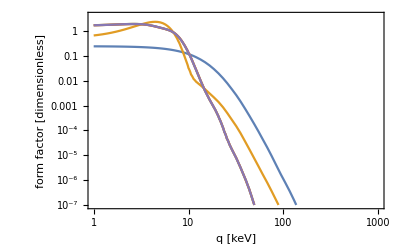

```mathematica
EtestkeV=0.025;

LogLogPlot[{fCH41a[q,EtestkeV],fCH42a[q,EtestkeV],fCH41tx[q,EtestkeV],fCH41ty[q,EtestkeV],fCH41tz[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

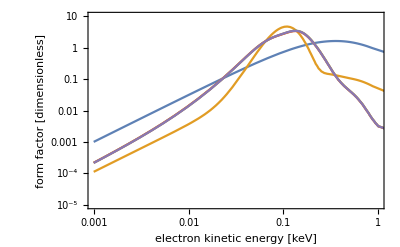

```mathematica
qtestkeV=10;

LogLogPlot[{fCH41a[qtestkeV,E1],fCH42a[qtestkeV,E1],fCH41tx[qtestkeV,E1],fCH41ty[qtestkeV,E1],fCH41tz[qtestkeV,E1]},{E1,0.001,1000},PlotRange->{{0.001,1},{10^-5,10}},Frame->True,FrameLabel->{"electron kinetic energy [keV]","form factor [dimensionless]"}]
```